```mathematica
Solution of the E-feld of a grounded conducting sphere (soild) under uniform E-field
```

```mathematica
Set 
E=E Subscript[e, z];
sphere radius = a;
Ψ(r>a)=-E z=-E r Cos[θ];
Ψ(r=R)= 0  // grounded;
field inside =0  // no field inside  ;
```

```mathematica
**********************************
```

```mathematica
choose spherical coordinate with no ϕ dependence
the Laplacian become :
∇^2 Ψ(r,θ)=(∂^2 Ψ)/(∂r^2)+2/r(∂Ψ)/(∂r)+1/(r^2 Sin[θ])∂/(∂θ)(Sin[θ](∂Ψ)/(∂θ))=0 ;
```

```mathematica
Set Ψ=R[r] P[θ]
```

```mathematica
P(∂^2 R)/(∂r^2)+P 2/r(∂R)/(∂r)+R/(r^2 Sin[θ])∂/(∂θ)(Sin[θ](∂P)/(∂θ))=0;
r^2/R(∂^2 R)/(∂r^2)+(2 r)/R(∂R)/(∂r)+1/(P Sin[θ])∂/(∂θ)(Sin[θ](∂P)/(∂θ))=0 // [divided by Ψ] such that Ψ≠0 and [times r^2];
r^2/R(∂^2 R)/(∂r^2)+(2 r)/R(∂R)/(∂r)=-k ; 1/(P Sin[θ])∂/(∂θ)(Sin[θ](∂P)/(∂θ))=k ;
```

```mathematica
****************************************
```

```mathematica
1/Sin[θ]∂/(∂θ)(Sin[θ](∂P)/(∂θ))=k P // Set u = Cos[θ] -> ⅆu=Sin[θ]ⅆθ, P[θ]-> P[u]
∂/(∂u)((1-u^2)(∂P)/(∂u))=k P // this is the Legendre differeatial equaetion;
the solution donate as LegendreP[l,u], ??? where l∈Ν, k=-l(l+1) ;
```

```mathematica
MatrixForm[Table[LegendreP[l,Cos[θ]],{l,0,7}]]
```

(1
Cos[θ]
1/2 (-1+3 Cos[θ]^2)
1/2 (-3 Cos[θ]+5 Cos[θ]^3)
1/8 (3-30 Cos[θ]^2+35 Cos[θ]^4)
1/8 (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)
1/16 (-5+105 Cos[θ]^2-315 Cos[θ]^4+231 Cos[θ]^6)
1/16 (-35 Cos[θ]+315 Cos[θ]^3-693 Cos[θ]^5+429 Cos[θ]^7))

```mathematica
*****************************************
```

```mathematica
r^2/R(∂^2 R)/(∂r^2)+(2 r)/R(∂R)/(∂r)=l(l+1) ; 
Try R=r^n;
r^n n(n-1)+2 r^n n=l(l+1) r^n ; 
n^2+n-l(l+1)=0;
```

```mathematica
FullSimplify[Solve[n^2+n-l(l+1)==0,n]]
```

{{n→-1-l},{n→l}}

```mathematica
The Solution of the Laplacian is:
Ψ[r,θ]=∑_(l=0)^∞ (Subscript[A, l] r^l+Subscript[B, l]/r^(l+1))LegendreP[l,u=Cos[θ]]
```

```mathematica
********************************************
```

```mathematica
For r<a, Subscript[B, l]=0 coz covergence, aussump it is hollow, if it is solid, than Ψ=0.
```

```mathematica
Ψ[r,θ]=∑_(l=0)^∞ Subscript[A, l] r^l LegendreP[l,Cos[θ]]
```

```mathematica
Boundary condition Ψ[a,θ]=0, and u=Cos[θ=0]=1
```

```mathematica
∑_(l=0)^∞ Subscript[A, l] a^l= 0
```

```mathematica
implie Subscript[A, l]=0;
```

```mathematica
^^^^^^^^^^^^^^^^
```

```mathematica
By property of Laplacian, no local maximum and minimum, the field inside must be zero.
```

```mathematica
^^^^^^^^^^^^^^^^
```

```mathematica
*******************************************
```

```mathematica
For r>a, Subscript[A, l]=0 coz covergence
```

```mathematica
Ψ[r,θ]=∑_(l=0)^∞ Subscript[B, l]/r^(l+1)LegendreP[l,Cos[θ]]-E r Cos[θ]
```

```mathematica
the only term that does not vanise by the orthgonlilty of the Legendre function is l=1
```

```mathematica
Ψ[a,θ]=-E a Cos[θ]+Subscript[B, 1]/a^2 Cos[θ]=0
```

```mathematica
Solve[-Ε a Cos[θ]+Subscript[B, 1]/a^2 Cos[θ]==0,Subscript[B, 1]]
```

{{B_1→a^3 Ε}}

```mathematica
Ψ[r,θ]=E (a^3/r^2-r)Cos[θ]
```

```mathematica
*****************************************
```

```mathematica
Ψ[r,θ]->Ψ[x,y];
(a^3/r^2-r)Cos[θ]/. r-> √(x^2+y^2)
```

```mathematica
(a^3/(x^2+y^2)-√(x^2+y^2)) Cos[θ]/. Cos[θ]-> x/(√(x^2+y^2))
```

```mathematica
FullSimplify[(x (a^3/(x^2+y^2)-√(x^2+y^2)))/(√(x^2+y^2))]
```

```mathematica
Plot3D[{x (-1+1/((x^2+y^2)^(3/2)))},{x,-2,2},{y,-2,2},AspectRatio->1,PlotRange-> {{-2,2},{-2,2},{-2,2}}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[{y/Tan[t] (-1+1/(((y/Tan[t])^2+y^2)^(3/2)))},{y,-2,2},AspectRatio->1,PlotRange-> {{-2,2},{-2,2}}],{t,0.01,π}]
```

```mathematica
FullSimplify[Grad[Xx (-1+1/((Xx^2+Yy^2)^(3/2))), Cartesian]]
```

```mathematica
{-1+(-2 Xx^2+Yy^2)/((Xx^2+Yy^2)^(5/2)),-(3 Xx Yy)/((Xx^2+Yy^2)^(5/2)),0}.{-1+(-2 Xx^2+Yy^2)/((Xx^2+Yy^2)^(5/2)),-(3 Xx Yy)/((Xx^2+Yy^2)^(5/2)),0}
```

```mathematica
FullSimplify[(9 Xx^2 Yy^2)/((Xx^2+Yy^2)^5)+(-1+(-2 Xx^2+Yy^2)/((Xx^2+Yy^2)^(5/2)))^2]
```

```mathematica
ContourPlot[(9 Xx^2 Yy^2)/((Xx^2+Yy^2)^5)+(-1+(-2 Xx^2+Yy^2)/((Xx^2+Yy^2)^(5/2)))^2,{Xx,-2,2},{Yy,-2,2},Exclusions->{Xx^2+Yy^2== 1},Contours->Function[{min,max},Range[min,max,0.1]]]
```

-Graphics-

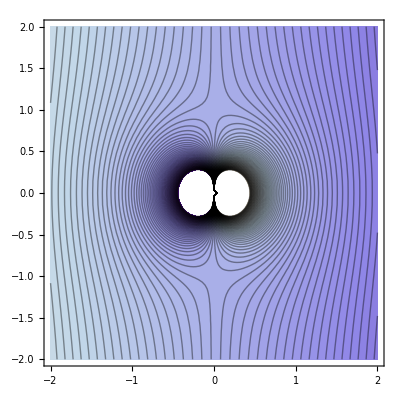

```mathematica
ContourPlot[Xx (-1+1/((Xx^2+Yy^2)^(3/2))),{Xx,-2,2},{Yy,-2,2},Exclusions->{Xx^2+Yy^2== 1},Contours->Function[{min,max},Range[min,max,0.1]]]
```

```mathematica
Needs["VectorFieldPlots`"]
```

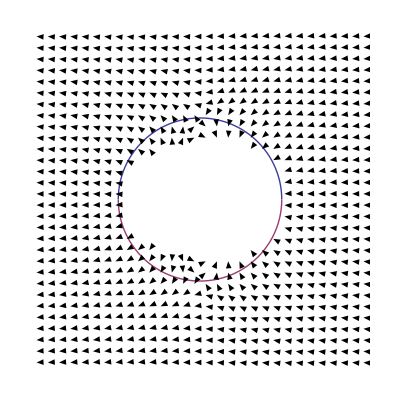

```mathematica
Show[VectorFieldPlot[{-1-(3 Xx^2)/((Xx^2+Yy^2)^(5/2))+1/((Xx^2+Yy^2)^(3/2)),-(3 Xx Yy)/((Xx^2+Yy^2)^(5/2))}, {Xx, -2, 2}, {Yy, -2, 2}, MaxArrowLength->3, PlotPoints -> 30] ,Plot[{√(1-(Xx)^2),-√(1-Xx^2)},{Xx,-1,1}]]
```

```mathematica
the charge density.
```

```mathematica
Laplacian[Xx (-1+1/((Xx^2+Yy^2)^(3/2))),Cartesian]
```

```mathematica
FullSimplify[(15 Xx^3)/((Xx^2+Yy^2)^(7/2))+(15 Xx Yy^2)/((Xx^2+Yy^2)^(7/2))-(12 Xx)/((Xx^2+Yy^2)^(5/2))]
```

(3 Xx)/((Xx^2+Yy^2)^(5/2))

```mathematica
(3 Xx)/((Xx^2+Yy^2)^(5/2))/.Xx->r Cos[t]
```

(3 r Cos[t])/((Yy^2+r^2 Cos[t]^2)^(5/2))

```mathematica
(3 r Cos[t])/((Yy^2+r^2 Cos[t]^2)^(5/2))/.Yy->r Sin[t]
```

```mathematica
Simplify[(3 r Cos[t])/((r^2 Cos[t]^2+r^2 Sin[t]^2)^(5/2))]
```

(3 r Cos[t])/((r^2)^(5/2))

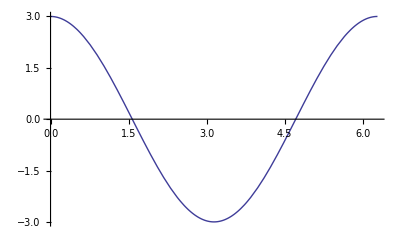

```mathematica
Plot[(15 Cos[t]^3)/((Cos[t]^2+Sin[t]^2)^(7/2))+(15 Cos[t] Sin[t]^2)/((Cos[t]^2+Sin[t]^2)^(7/2))-(12 Cos[t])/((Cos[t]^2+Sin[t]^2)^(5/2)),{t,0,2 π}]
```

```mathematica
Plot3D[(15 Xx^3)/((Xx^2+Yy^2)^(7/2))+(15 Xx Yy^2)/((Xx^2+Yy^2)^(7/2))-(12 Xx)/((Xx^2+Yy^2)^(5/2)),{Xx,-2,2},{Yy,-2,2}]
```

-Graphics3D-

```mathematica
the surface charge density, σ=(∂Ψ)/(∂r) at r=a
```

```mathematica
D[-(a^3/r^2-r)Cos[θ],r]
```

```mathematica
this give out the E field
```

```mathematica
-(-1-(2 a^3)/r^3) Cos[θ]/.r->a
```

3 Cos[θ]

```mathematica
*******************************************************
```

```mathematica
*******************************************************
```

```mathematica
for dielectric sphere
```

```mathematica
Ψ[r,θ]=∑_(l=0)^∞ Subscript[A, l] r^l LegendreP[l,Cos[θ]]// r<a
```

```mathematica
Ψ[r,θ]=∑_(l=0)^∞ Subscript[B, l]/r^(l+1)LegendreP[l,Cos[θ]]-Ε r Cos[θ] // r>a
```

```mathematica
∑_(l=0)^∞ Subscript[A, l] a^l LegendreP[l,Cos[θ]] =0=∑_(l=0)^∞ Subscript[B, l]/a^(l+1)LegendreP[l,Cos[θ]]-E r Cos[θ] // r=a
```

```mathematica
Ε=-∇Ψ
```

```mathematica
the Boundary condition is Subscript[Ε, θ] , Subscript[D, r] continous
```

```mathematica
*******************************************
```

```mathematica
the Fast way to do
```

```mathematica
Ψ[r,θ]=A r Cos[θ]// r<a,
```

```mathematica
Ψ[r,θ]=B/r^2 Cos[θ]-Ε r Cos[θ] // r>a
```

```mathematica
because the external field only contain LegendreP[1, Cos[θ]], if add higher order therm, than by the orthogolilty of the LegendreP fuction and Sin-Cos seriers, they will cancell out.
```

```mathematica
the Physical reason for that is, 
there is no uniform field, so Ψ=constant =0
no point source, 1/r term =0
since the delectric or the metal sphere, will be induced some charge on the surface and created a dipole, Cos[θ]/r^2  left
and there is no Quripole and higher multi-pole, so the rest =0
```

```mathematica
for r<a
```

```mathematica
Subscript[D, r]=ϵ Subscript[Ε, r]=-A ϵ Cos[θ]
```

```mathematica
Subscript[Ε, θ]=A Sin[θ]
```

```mathematica
for r>a
```

```mathematica
Subscript[D, r]=Subscript[Ε, r]= (2B)/r^3 Cos[θ]+E Cos[θ]
```

```mathematica
Subscript[Ε, θ]= B/r^3 Sin[θ]-E Sin[θ]
```

```mathematica
- A ϵ= (2B)/a^3+E
```

```mathematica
A=B/a^3-E
```

```mathematica
Solve[ (2B)/a^3+E == -ϵ (B/a^3-E ),B]
```

{{B→(a^3 (-ⅇ+ⅇ ϵ))/(2+ϵ)}}

```mathematica
B=Ε a^3 (ϵ-1)/(ϵ+2)
```

```mathematica
Simplify[Ε  (ϵ-1)/(ϵ+2)-Ε]
```

-(3 Ε)/(2+ϵ)

```mathematica
A=-Ε 3/(ϵ+2)
```

```mathematica
Ψ[r,θ]=- Ε 3/(ϵ+2)r Cos[θ]// r<a,
```

```mathematica
Ψ[r,θ]=Ε ( (ϵ-1)/(ϵ+2)a^3/r^2- r) Cos[θ] // r>a
```

```mathematica
Manipulate[Plot[{-3/(ϵ+2)r Cos[θ],( (ϵ-1)/(ϵ+2)1/r^2- r) Cos[θ] },{r,0.01,2}],{θ,0,π},{ϵ,1,10}]
```

```mathematica
****************************************
```

```mathematica
Needs["VectorFieldPlots`"]
```

```mathematica
( (ϵ-1)/(ϵ+2)a^3/r^2- r) Cos[θ] /.{r->Rr, θ->Ttheta}
```

```mathematica
Simplify[Laplacian[(-Rr+(a^3 (-1+ϵ))/(Rr^2 (2+ϵ))) Cos[Ttheta], Spherical]]
```

0

```mathematica
Ψ[r,θ]->Ψ[x,y]
```

```mathematica
Simplify[( (ϵ-1)/(ϵ+2)a^3/r^2- r) Cos[θ] /.{r-> √(x^2+y^2+z^2),Cos[θ]-> x/(√(x^2+y^2+z^2)),a->1,ϵ->2}]
```

1/4 x (-4+1/((x^2+y^2+z^2)^(3/2)))

```mathematica
-(x (-1+4 (x^2+y^2)^(3/2)))/(4 (x^2+y^2)^(3/2)) // the potential function in cartesian coordinate, ϵ = 2, E=1
```

```mathematica
1/4 x (-4+1/((x^2+y^2+z^2)^(3/2)))/.{x->Xx,y->Yy,z->Zz}
```

1/4 Xx (-4+1/((Xx^2+Yy^2+Zz^2)^(3/2)))

```mathematica
Simplify[Laplacian[1/4 Xx (-4+1/((Xx^2+Yy^2+Zz^2)^(3/2))),Cartesian]]
```

0

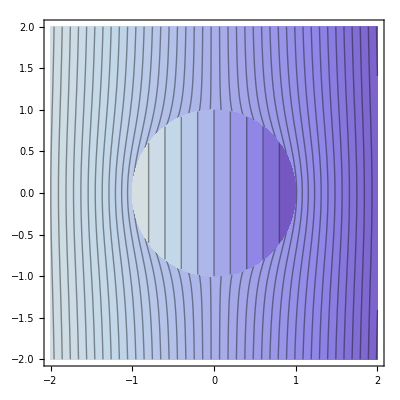

```mathematica
Show[ContourPlot[{-(x (-1+4 (x^2+y^2)^(3/2)))/(4 (x^2+y^2)^(3/2))},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y},x^2+y^2>1],Contours->Function[{min,max},Range[min,max,0.1]]],
ContourPlot[{-x/2},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y},x^2+y^2<1],Contours->Function[{min,max},Range[min,max,0.1]]]]
```

```mathematica
************************
```

```mathematica
Other way
```

```mathematica
for r<a
```

```mathematica
Subscript[D, r]=ϵ Subscript[Ε, r]=-∑_(l=0)^∞ Subscript[A, l] ϵ l r^(l-1)LegendreP[l,Cos[θ]]
```

```mathematica
Subscript[Ε, θ]=-∑_(l=0)^∞ Subscript[A, l] r^(l-1)ⅆ/ⅆθ LegendreP[l,Cos[θ]]
```

```mathematica
************************
```

```mathematica
for r>a
```

```mathematica
Subscript[D, r]=Subscript[Ε, r]=∑_(l=0)^∞ Subscript[B, l]/r^(l+2) (l+1)LegendreP[l,Cos[θ]]+Ε Cos[θ]
```

```mathematica
Subscript[Ε, θ]=-∑_(l=0)^∞ Subscript[B, l]/r^(l+2)ⅆ/ⅆθ LegendreP[l,Cos[θ]]-Ε  Sin[θ]
```

```mathematica
*****************************************
```

```mathematica
-∑_(l=0)^∞ Subscript[A, l] ϵ l a^(l-1)LegendreP[l,Cos[θ]]=∑_(l=0)^∞ Subscript[B, l]/a^(l+2) (l+1)LegendreP[l,Cos[θ]]+Ε Cos[θ]
```

```mathematica
FullSimplify[MatrixForm[Table[Subscript[A, l] ϵ l a^(l-1)LegendreP[l,Cos[θ]]+Subscript[B, l]/a^(l+2) (l+1)LegendreP[l,Cos[θ]]+Ε Cos[θ]==0,{l,0,5}]]]
```

(Ε Cos[θ]+B_0/a^2==0
Cos[θ] (Ε+ϵ A_1+(2 B_1)/a^3)==0
Ε Cos[θ]+((1+3 Cos[2 θ]) (2 a^5 ϵ A_2+3 B_2))/(4 a^4)==0
(8 a^5 Ε Cos[θ]+(3 Cos[θ]+5 Cos[3 θ]) (3 a^7 ϵ A_3+4 B_3))/a==0
(64 a^6 Ε Cos[θ]+4 a^9 ϵ (9+20 Cos[2 θ]+35 Cos[4 θ]) A_4+5 (9+20 Cos[2 θ]+35 Cos[4 θ]) B_4)/a==0
1/8 Cos[θ] (8 Ε+((15-70 Cos[θ]^2+63 Cos[θ]^4) (5 a^11 ϵ A_5+6 B_5))/a^7)==0)

```mathematica
only l=1 left
```

```mathematica
(Ε+ϵ Subscript[A, 1]+(2 Subscript[B, 1])/a^3)=0
```

```mathematica
2 a^5 ϵ Subscript[A, 2]+3 Subscript[B, 2]=0
```

```mathematica
****************************
```

```mathematica
∑_(l=0)^∞ Subscript[A, l] a^(l-1)ⅆ/ⅆθ LegendreP[l,Cos[θ]]=∑_(l=0)^∞ Subscript[B, l]/a^(l+2)ⅆ/ⅆθ LegendreP[l,Cos[θ]]+Ε  Sin[θ]
```

```mathematica
FullSimplify[MatrixForm[Table[(Subscript[A, l] a^(l-1)-Subscript[B, l]/a^(l+2)) D[LegendreP[l,Cos[θ]],θ]==Ε Sin[θ],{l,0,5}]]]
```

(Ε Sin[θ]==0
Sin[θ] (-A_1+B_1/a^3)==Ε Sin[θ]
(3 Cos[θ] Sin[θ] (-a^5 A_2+B_2))/a^4==Ε Sin[θ]
(3 (Sin[θ]+5 Sin[3 θ]) (-a^7 A_3+B_3))/(8 a^5)==Ε Sin[θ]
(5 (2 Sin[2 θ]+7 Sin[4 θ]) (-a^9 A_4+B_4))/(16 a^6)==Ε Sin[θ]
(15 (2 Sin[θ]+7 (Sin[3 θ]+3 Sin[5 θ])) (-a^11 A_5+B_5))/(128 a^7)==Ε Sin[θ])

```mathematica
Since 0 == E Sin[θ] is non-sence
the l=0 should be vanish at the very begining, therefore no order zero term.
```

```mathematica
Subscript[A, 1]=Subscript[B, 1]/a^3-E
```

```mathematica
the others terms are also non-sence, the only choice of A and B is zero.
```

```mathematica
-3 Cos[θ]  (a Subscript[A, 2]-Subscript[B, 2]/a^4)==Ε , integrate both side by Cos[θ] from 0 to π
```

```mathematica
Subscript[A, 2]=Subscript[B, 2]/a^5
```

```mathematica
********************
```

```mathematica
Ε+ϵ Subscript[A, 1]+(2 Subscript[B, 1])/a^3=0
```

```mathematica
Subscript[A, 1]=Subscript[B, 1]/a^3-E
```

```mathematica
Solve[Ε+ϵ (Subscript[B, 1]/a^3-Ε)+(2 Subscript[B, 1])/a^3==0, Subscript[B, 1]]
```

{{B_1→(a^3 (-Ε+ϵ Ε))/(2+ϵ)}}

```mathematica
Simplify[((a^3 (-Ε+ϵ Ε))/(2+ϵ))/a^3-Ε]
```

```mathematica
Subscript[A, 1]=-(3 Ε)/(2+ϵ)
```

```mathematica
*************************************
Surface charge Density
```

```mathematica
Surface charge σ=P=(D- Ε)=(ϵ-1)E
```

```mathematica
Ψ[r,θ]=- Ε 3/(ϵ+2)r Cos[θ]// r<a,
```

```mathematica
Ψ[r,θ]=Ε ( (ϵ-1)/(ϵ+2)a^3/r^2- r) Cos[θ] // r>a
it contains r Cos[θ] = Uniform field
Cos[θ]/r^2=dipole moment
```

```mathematica
from potential to E-field line
```

```mathematica
Φ[x,y]=-(x (-1+4 (x^2+y^2)^(3/2)))/(4 (x^2+y^2)^(3/2)) // ϵ=2, a=1
```

```mathematica
FullSimplify[D[1/4 x (-4+1/((x^2+y^2)^(3/2))),{x,2}]+D[1/4 x (-4+1/((x^2+y^2)^(3/2))),{y,2}]]
```

(3 x)/(4 (x^2+y^2)^(5/2))

```mathematica
Integrate[- D[1/4 x (-4+1/((x^2+y^2)^(3/2))),x],y]+Integrate[ D[1/4 x (-4+1/((x^2+y^2)^(3/2))),y],x]
```

```mathematica
FullSimplify[y+y/(4 (x^2+y^2)^(3/2))-y/(4 x^2 √(x^2+y^2))+3/4 x^2 √(x^2+y^2) (y/(3 x^2 (x^2+y^2)^2)+(2 y)/(3 x^4 (x^2+y^2)))]
```

```mathematica
1/4 y (4+2/((x^2+y^2)^(3/2))+1/(x^2 √(x^2+y^2)))
```

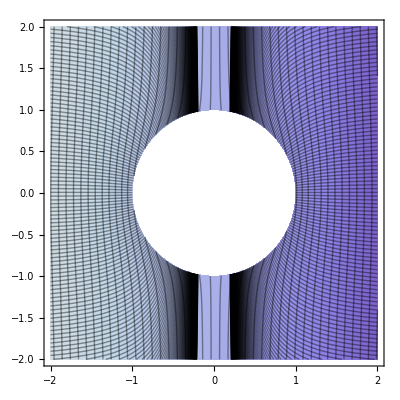

```mathematica
Show[ContourPlot[-(x (-1+4 (x^2+y^2)^(3/2)))/(4 (x^2+y^2)^(3/2)),{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y},x^2+y^2>1],Contours->Function[{min,max},Range[min,max,0.1]]],ContourPlot[1/4 y (4+2/((x^2+y^2)^(3/2))+1/(x^2 √(x^2+y^2))),{x,-2,2},{y,-2,2},ContourShading->None,RegionFunction->Function[{x,y},x^2+y^2>1],Contours->Function[{min,max},Range[min,max,0.1]]]]
```

```mathematica
Plot ALL
```

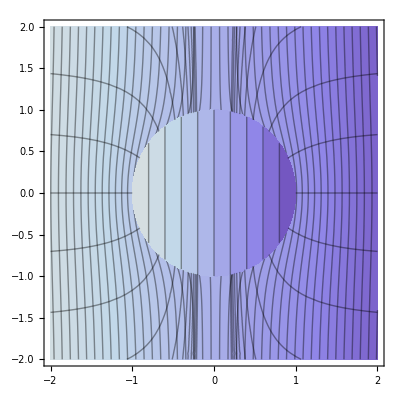

```mathematica
Show[ContourPlot[{-(x (-1+4 (x^2+y^2)^(3/2)))/(4 (x^2+y^2)^(3/2))},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y},x^2+y^2>1],Contours->Function[{min,max},Range[min,max,0.1]]],ContourPlot[{-x/2},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y},x^2+y^2<1],Contours->Function[{min,max},Range[min,max,0.1]]],ContourPlot[y/(4 (x^2+y^2)^(3/2))+1/4 y (4+(2 x^2+y^2)/(x^2 (x^2+y^2)^(3/2))),{x,-2,2},{y,-2,2},ContourShading->None,RegionFunction->Function[{x,y},x^2+y^2>1],Contours->20]]
```